```mathematica
(* Estimation of the probability of bound violation *)
```

```mathematica
(* Population initialization *)
```

```mathematica
init[m_,n_,a_,b_]:=Module[{p},p=Table[Random[Real,{a[[j]],b[[j]]}],{i,m},{j,n}]; Return[p]];
```

```mathematica
(* Best element in the population *)
```

```mathematica
best[v_]:=Module[{imin=1,m=Length[v]},Do[If[v[imin]>v[i],imin=i],{i,1,m}];Return[imin]];
```

```mathematica
(* Computation of the mutation probability depending on the crossover type *)
```

```mathematica
pmBin[CR_,n_]:= CR*(1-1/n)+1/n
```

```mathematica
pmExp[CR_,n_]:= If[CR==1,1,(1-CR^n)/(n*(1-CR))]
```

```mathematica
(* Reproduction based on DE/rand/1/bin and uniform reinitialization of infeasible components *)
```

```mathematica
reproductionDErand1Uniform[p_,i_,CR_,F_,a_,b_,tipCrossover_]:=Module[{x1,x2,x3,i1,i2,i3,m,y,pm,n,countViolations=0,countViolations2},m=Length[p];n=Length[p[[1]]]; i1=Random[Integer,{1,m}]; While[i1==i, i1=Random[Integer,{1,m}]];
i2=Random[Integer,{1,m}]; While[i2==i || i2==i1, i2=Random[Integer,{1,m}]];
i3=Random[Integer,{1,m}]; While[i3==i || i3==i1 || i3==i2, i3=Random[Integer,{1,m}]];
y=p[[i1]]+F*(p[[i2]]-p[[i3]]);
pm=If[tipCrossover==0,pmBin[CR,n],pmExp[CR,n]];
Do[If[(y[[j]]<a[[j]])||(y[[j]]>b[[j]]),countViolations=countViolations+1;y[[j]]=Random[Real,{a[[j]],b[[j]]}]],{j,1,n}];
Do[y[[j]]=If[Random[]<pm,y[[j]],p[[i,j]]],{j,1,n}]; 
Return [{countViolations,y}]];
```

```mathematica
(* Reproduction based on DE/rand/1/bin and correction of infeasible components by saturation *)
```

```mathematica
reproductionDErand1Saturate[p_,i_,CR_,F_,a_,b_,tipCrossover_]:=Module[{x1,x2,x3,i1,i2,i3,m,y,pm,n,countViolations=0,countViolations2},m=Length[p];n=Length[p[[1]]]; i1=Random[Integer,{1,m}]; While[i1==i, i1=Random[Integer,{1,m}]];
i2=Random[Integer,{1,m}]; While[i2==i || i2==i1, i2=Random[Integer,{1,m}]];
i3=Random[Integer,{1,m}]; While[i3==i || i3==i1 || i3==i2, i3=Random[Integer,{1,m}]];
y=p[[i1]]+F*(p[[i2]]-p[[i3]]);
pm=If[tipCrossover==0,pmBin[CR,n],pmExp[CR,n]];
Do[If[(y[[j]]<a[[j]])||(y[[j]]>b[[j]]),countViolations=countViolations+1;y[[j]]=If[y[[j]]<a[[j]],a[[j]],b[[j]]]],{j,1,n}];
Do[y[[j]]=If[Random[]<pm,y[[j]],p[[i,j]]],{j,1,n}]; 
Return [{countViolations,y}]];
```

```mathematica
(* Reproduction based on DE/rand/1/bin and correction of infeasible components by mirroring *)
```

```mathematica
reproductionDErand1Mirror[p_,i_,CR_,F_,a_,b_,tipCrossover_]:=Module[{x1,x2,x3,i1,i2,i3,m,y,pm,n,countViolations=0,countViolations2},m=Length[p];n=Length[p[[1]]]; i1=Random[Integer,{1,m}]; While[i1==i, i1=Random[Integer,{1,m}]];
i2=Random[Integer,{1,m}]; While[i2==i || i2==i1, i2=Random[Integer,{1,m}]];
i3=Random[Integer,{1,m}]; While[i3==i || i3==i1 || i3==i2, i3=Random[Integer,{1,m}]];
y=p[[i1]]+F*(p[[i2]]-p[[i3]]);
pm=If[tipCrossover==0,pmBin[CR,n],pmExp[CR,n]];
Do[If[(y[[j]]<a[[j]])||(y[[j]]>b[[j]]),countViolations=countViolations+1],{j,1,n}];
Do[While[y[[j]]<a[[j]]||y[[j]]>b[[j]],If[y[[j]]<a[[j]],y[[j]]=2*a[[j]]-y[[j]],y[[j]]=2*b[[j]]-y[[j]]]],{j,1,n}];
Do[y[[j]]=If[Random[]<pm,y[[j]],p[[i,j]]],{j,1,n}]; 
Return [{countViolations,y}]];
```

```mathematica
(* Reproduction based on DE/rand/1/bin and correction of infeasible components by toroidal reflection *)
```

```mathematica
reproductionDErand1Toroidal[p_,i_,CR_,F_,a_,b_,tipCrossover_]:=Module[{x1,x2,x3,i1,i2,i3,m,y,pm,n,countViolations=0,countViolations2},m=Length[p];n=Length[p[[1]]]; i1=Random[Integer,{1,m}]; While[i1==i, i1=Random[Integer,{1,m}]];
i2=Random[Integer,{1,m}]; While[i2==i || i2==i1, i2=Random[Integer,{1,m}]];
i3=Random[Integer,{1,m}]; While[i3==i || i3==i1 || i3==i2, i3=Random[Integer,{1,m}]];
y=p[[i1]]+F*(p[[i2]]-p[[i3]]);
pm=If[tipCrossover==0,pmBin[CR,n],pmExp[CR,n]];
Do[If[(y[[j]]<a[[j]])||(y[[j]]>b[[j]]),countViolations=countViolations+1],{j,1,n}];
Do[While[y[[j]]<a[[j]]||y[[j]]>b[[j]],If[y[[j]]<a[[j]],y[[j]]=b[[j]]-(a[[j]]-y[[j]]),y[[j]]=a[[j]]+(y[[j]]-b[[j]])]],{j,1,n}];
Do[y[[j]]=If[Random[]<pm,y[[j]],p[[i,j]]],{j,1,n}]; 
Return [{countViolations,y}]];
```

```mathematica
(*COTNupper:=TruncatedDistribution[{-2,0},NormalDistribution[]];
COTNlower:=TruncatedDistribution[{0,2},NormalDistribution[]];*)reproductionDErand1COTN[p_,i_,CR_,F_,a_,b_,tipCrossover_]:=Module[{x1,x2,x3,i1,i2,i3,m,y,pm,n,countViolations=0,countViolations2},m=Length[p];n=Length[p[[1]]]; i1=Random[Integer,{1,m}]; While[i1==i, i1=Random[Integer,{1,m}]];
i2=Random[Integer,{1,m}]; While[i2==i || i2==i1, i2=Random[Integer,{1,m}]];
i3=Random[Integer,{1,m}]; While[i3==i || i3==i1 || i3==i2, i3=Random[Integer,{1,m}]];
y=p[[i1]]+F*(p[[i2]]-p[[i3]]);
pm=If[tipCrossover==0,pmBin[CR,n],pmExp[CR,n]];
Do[If[(y[[j]]<a[[j]])||(y[[j]]>b[[j]]),countViolations=countViolations+1;
y[[j]]=If[y[[j]]<a[[j]],a[[j]]+(b[[j]]-a[[j]])*Abs[RandomVariate[NormalDistribution[]]]/3,a[[j]]+(b[[j]]-a[[j]])*Abs[1-Abs[RandomVariate[NormalDistribution[]]]/3]]],{j,1,n}];
Do[y[[j]]=If[Random[]<pm,y[[j]],p[[i,j]]],{j,1,n}]; 
Return [{countViolations,y}]];
```

```mathematica
(* Reproduction based on DE/rand/1/bin and correction of infeasible components by midpoint target *)
reproductionDErand1MidpointTarget[p_,i_,CR_,F_,a_,b_,tipCrossover_]:=Module[{x1,x2,x3,i1,i2,i3,m,y,pm,n,countViolations=0,countViolations2},m=Length[p];n=Length[p[[1]]]; i1=Random[Integer,{1,m}]; While[i1==i, i1=Random[Integer,{1,m}]];
i2=Random[Integer,{1,m}]; While[i2==i || i2==i1, i2=Random[Integer,{1,m}]];
i3=Random[Integer,{1,m}]; While[i3==i || i3==i1 || i3==i2, i3=Random[Integer,{1,m}]];
y=p[[i1]]+F*(p[[i2]]-p[[i3]]);
pm=If[tipCrossover==0,pmBin[CR,n],pmExp[CR,n]];
Do[If[(y[[j]]<a[[j]])||(y[[j]]>b[[j]]),countViolations=countViolations+1;y[[j]]=If[y[[j]]<a[[j]],(a[[j]]+p[[i,j]])/2,(b[[j]]+p[[i,j]])/2]],{j,1,n}];
Do[y[[j]]=If[Random[]<pm,y[[j]],p[[i,j]]],{j,1,n}]; 
Return [{countViolations,y}]];
```

```mathematica
(* computation of the variance *)
```

```mathematica
var[x_]:=Mean[x^2]-Mean[x]^2; variance[p_]:=Module[{c,v},c=Map[var,Transpose[p]];v=Mean[c]; Return[v]]
```

```mathematica
(* DE evolution - it returns only the list with estimated bound violation probabilities over gen generations *)
```

```mathematica
DE[m_,n_,CR_,F_,a_,b_,gen_,crossoverType_,correctionType_, eval_,runs_]:=Module[{p,v,y,vy, ibest,countViolations,cv,vbest, varPop,ViolProb, meanViolProb={}},
Do[p=init[m,n,a,b]; v=Table[eval[p[[i]]],{i,1,m}]; ibest=best[v]; countViolations=Table[0,{gen}];
vbest=Table[0,{gen}];
varPop=Table[0,{gen}];
Do[Do[
{cv,y}=Which[correctionType=="unif",reproductionDErand1Uniform[p,i,CR,F,a,b,crossoverType], correctionType=="saturate",
reproductionDErand1Saturate[p,i,CR,F,a,b,crossoverType],correctionType=="mirror",reproductionDErand1Mirror[p,i,CR,F,a,b,crossoverType],correctionType=="toroidal",
reproductionDErand1Toroidal[p,i,CR,F,a,b,crossoverType],correctionType=="cotn",
reproductionDErand1COTN[p,i,CR,F,a,b,crossoverType]];
countViolations[[g]]=countViolations[[g]]+cv; 
vy=eval[y]; If[vy<=v[[i]],p[[i]]=y;v[[i]]=vy],{i,1,m}]; 
ibest=best[v]; vbest[[g]]=v[[ibest]];
varPop[[g]]=variance[p];,{g,1,gen}];
ViolProb=N[countViolations/(m*n)];
meanViolProb=Append[meanViolProb,Mean[ViolProb]],{runs}];Return[meanViolProb]]
```

```mathematica
(* test functions - f0, flat *)
```

```mathematica
inf=Table[-10,{100}]; sup=Table[10,{100}];
flat[x_]:=1;
f0[x_]:=Random[]
```

```mathematica
(* List of the values of F and CR *)
```

```mathematica
listF={0.05,0.285,0.52,0.755,0.99}; listCR={0.05,0.285,0.52,0.755,0.99};
```

```mathematica
(* Computation of the mean over generations of the violation probability *)
```

```mathematica
m=100; n=30; gen=100; runs=50;
```

```mathematica
pvUnifCR099range10=Table[Mean[DE[m,n,listCR[[5]],listF[[indF]],inf,sup,gen,0,"unif",f0,runs]],{indF,1,Length[listF]}];
```

```mathematica
pvSaturateCR099=Table[Mean[DE[m,n,listCR[[5]],listF[[indF]],inf,sup,gen,0,"saturate",f0,runs]],{indF,1,Length[listF]}];
```

```mathematica
pvMirrorCR099=Table[Mean[DE[m,n,listCR[[5]],listF[[indF]],inf,sup,gen,0,"mirror",f0,runs]],{indF,1,Length[listF]}];
```

```mathematica
pvToroidalCR099=Table[Mean[DE[m,n,listCR[[5]],listF[[indF]],inf,sup,gen,0,"toroidal",f0,runs]],{indF,1,Length[listF]}];
```

```mathematica
pvCotnCR099=Table[Mean[DE[m,n,listCR[[5]],listF[[indF]],inf,sup,gen,0,"cotn",f0,runs]],{indF,1,Length[listF]}];
```

```mathematica
colors={{0.4,0.7607843137254902,0.6470588235294118},{0.9882352941176471,0.5529411764705883,0.3843137254901961},{0.5529411764705883,0.6274509803921569,0.796078431372549},{0.9058823529411765,0.5411764705882353,0.7647058823529411},{0.6509803921568628,0.8470588235294118,0.32941176470588235},{0.8980392156862745,0.7686274509803922,0.5803921568627451}};
```

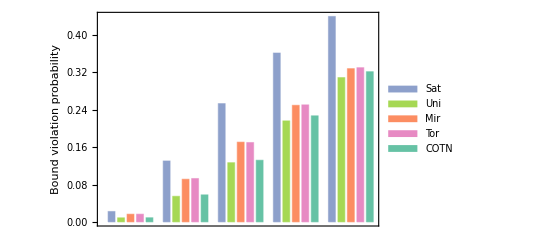

```mathematica
gBarChart=BarChart[Transpose[{pvSaturateCR099,pvUnifCR099range10,pvMirrorCR099,pvToroidalCR099,pvCotnCR099}],ChartLegends->Placed[{"Sat","Uni","Mir","Tor","COTN"},{Left,Top}],Frame->True,FrameLabel->{"","Bound violation probability"},ChartStyle->{RGBColor[colors[[3]]],RGBColor[colors[[5]]],RGBColor[colors[[2]]],RGBColor[colors[[4]]],RGBColor[colors[[1]]]}]
```

```mathematica
(* Theoretical limits for the violation probability - saturate (BoundViolationProbabilitySaturation.nb *)
```

```mathematica
pvTheoretical=(listF/3.0)
```

{0.0166667,0.095,0.173333,0.251667,0.33}

```mathematica
pvTheoretical23=(2*listF/3.0)
```

{0.0333333,0.19,0.346667,0.503333,0.66}

```mathematica
xlin={1.1,7,12.9,18.6,24.5};lg=5;r=0.01;lin005=Graphics[{Dashing[{r,r}],Line[{{xlin[[1]],pvTheoretical[[1]]},{xlin[[1]]+lg,pvTheoretical[[1]]}}],Line[{{xlin[[1]],pvTheoretical23[[1]]},{xlin[[1]]+lg,pvTheoretical23[[1]]}}]}]; lin0285=Graphics[{Dashing[{r,r}],Line[{{xlin[[2]],pvTheoretical[[2]]},{xlin[[2]]+lg,pvTheoretical[[2]]}}],Line[{{xlin[[2]],pvTheoretical23[[2]]},{xlin[[2]]+lg,pvTheoretical23[[2]]}}]}];
lin052=Graphics[{Dashing[{r,r}],Line[{{xlin[[3]],pvTheoretical[[3]]},{xlin[[3]]+lg,pvTheoretical[[3]]}}],Line[{{xlin[[3]],pvTheoretical23[[3]]},{xlin[[3]]+lg,pvTheoretical23[[3]]}}]}];
lin0755=Graphics[{Dashing[{r,r}],Line[{{xlin[[4]],pvTheoretical[[4]]},{xlin[[4]]+lg,pvTheoretical[[4]]}}],Line[{{xlin[[4]],pvTheoretical23[[4]]},{xlin[[4]]+lg,pvTheoretical23[[4]]}}]}];
lin099=Graphics[{Dashing[{r,r}],Line[{{xlin[[5]],pvTheoretical[[5]]},{xlin[[5]]+lg,pvTheoretical[[5]]}}],Line[{{xlin[[5]],pvTheoretical23[[5]]},{xlin[[5]]+lg,pvTheoretical23[[5]]}}]}];
```

```mathematica
gtest=Graphics[{Text[Style["F=0.05",Medium],{xlin[[1]]+lg/2,0.055}],Text[Style["F=0.285",Medium],{xlin[[2]]+lg/2,0.16}],Text[Style["F=0.52",Medium],{xlin[[3]]+lg/2,0.3}],Text[Style["F=0.755",Medium],{xlin[[4]]+lg/2,0.4}],Text[Style["F=0.99",Medium],{xlin[[5]]+lg/2,0.46}]}];
```

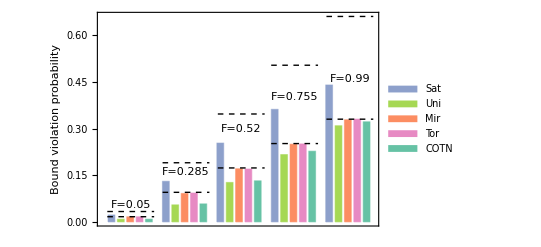

```mathematica
Show[gBarChart,lin005,lin0285,lin052,lin0755,lin099,gtest]
```